## Part 3 - Descriptive Analysis

Mean

Below is a point estimate for US GDP from 1990-2009 along with its 2-sided confidence interval at the α=.95 level. This corresponds to t_α being {-2.086,2.086} for the lower and upper bounds, respectively.

```mathematica
pointestimate
```

9.79957×10^12

```mathematica
moeusgdp
```

6.53424×10^11

```mathematica
{pointestimate-(2.086*moeusgdp),pointestimate+(2.086*moeusgdp)}
```

{8.43653×10^12,1.11626×10^13}

I decided that an important figure for the US to be at as far as the mean gdp goes is >  the national budget. In 2010 that figure was 3.522 E12 USD. I want to give the US a chance and test at the 99% level which corresponds to a one-sided test statistic of -2.539

H_0:μ=3.522e 12
H_a: μ < 3.522 e 12

(x^--μ)/(√(s^2/n))~t(n-1) → t-score

```mathematica
(Mean[usgdp]-3.522*10^12)/(√(Variance[usgdp]/20))
```

9.60719

```mathematica
9.60719>-2.539
```

True

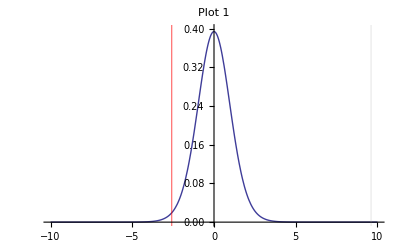

```mathematica
plot1=Plot[PDF[StudentTDistribution[19],x],{x,-10,10},GridLines->{{{-2.58,Red},{9.60719,{Dashed,Thick}}},{1}},PlotRange->{0,.4},PlotLabel->"Plot 1"]
```

In this plot the dashed line represents our test statistic of 9.60719 and the red line represets the rejection region. We are clearly not in the rejection region so we fail to reject H_0 that the real μ for US GDP is = the national budget. Because of how we formed our null hypothesis we can interpret the = sign in H_0 to mean ≥.

```mathematica
1-CDF[StudentTDistribution[19],9.60719]
```

4.99836×10^-9

The p-value associated with the test statittic I calculated is 4.99 E -10.

Range of Values: I want to test to see what the probablity is that μ is between 8 Trillion dollars and 15 trillion dollars

```mathematica
{(Mean[usgdp]-8*10^12)/(√(Variance[usgdp]/20)),(Mean[usgdp]-15*10^12)/(√(Variance[usgdp]/20))}
```

{2.75406,-7.95874}

```mathematica
CDF[StudentTDistribution[19],2.75]
```

```mathematica
0.9936325172254324
```

```mathematica
CDF[StudentTDistribution[19],-7.95874]
```

9.04794×10^-8

```mathematica
CDF[StudentTDistribution[19],2.75]-CDF[StudentTDistribution[19],-7.95874]
```

0.993632

This means that the probabliity that the true mean is between 8 and 15 trillion dollars is 0.993632.

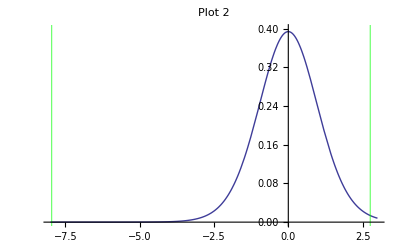

```mathematica
plot2=Plot[PDF[StudentTDistribution[19],x],{x,-8,3},GridLines->{{{-7.95784,Green},{2.75404,Green}},{1}},PlotRange->{0,.4},PlotLabel->"Plot 2"]
```

The area we are interested in is between the red lines.

Variance

### Below is the estimate of Variance along with a confidence interval at an α level of .95

```mathematica
Variance[usgdp]
```

8.53926×10^24

((n-1)(S^2))/(α-score)

```mathematica
(19)*(8.539258686421052*^24)/30.1435
```

5.38245×10^24

The range of expected values for Variance is between [5.38245×10^24,∞]

### Preform a hypothesis test that σ^2= a certain value

The value I chose to test for σ^2is 10 E 24

H_o:σ^2=10E 24
H_a:σ^2> 10 E 24
α=.90, corresponding χ^2 value is 27.2036

((n-1)(S^2))/σ^2→ χ^2(n-1)

```mathematica
((19)(Variance[usgdp]))/(10 * 10^24)
```

16.2246

```mathematica
1-CDF[ChiSquareDistribution[19],16.2246]
```

0.642244

The p-Value associated with our estimate of variance is .642244.

The test statistic is not in the rejection region so we cannot reject the null hypothesis that hte variance is = (≤)10 E 24.

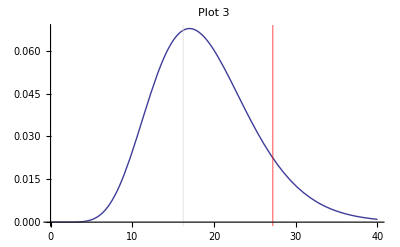

```mathematica
plot3=Plot[PDF[ChiSquareDistribution[19],x],{x,0,40},GridLines->{{{16.2246,{Dashed,Thick}},{27.2036,Red}},{0}},PlotLabel->"Plot 3"]
```

In the plot the red line represents the rejection region and the dashed line is our test statistic.

### A range of values for variance: P(5 *10^24≤σ^2≤12 *10^24)

```mathematica
((19)*(Variance[usgdp]))/(12*10^24)
```

13.5205

```mathematica
((19)*(Variance[usgdp]))/(5*10^24)
```

32.4492

```mathematica
CDF[ChiSquareDistribution[19],13.5205]
```

0.189108

```mathematica
CDF[ChiSquareDistribution[19],32.4492]
```

0.972199

```mathematica
0.9721993462124298-0.18910768006177409
```

0.783092

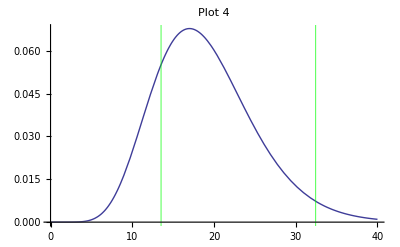

```mathematica
plot4=Plot[PDF[ChiSquareDistribution[19],x],{x,0,40},GridLines->{{{13.5205,Green},{32.4492,Green}},{0}},PlotLabel->"Plot 4"]
```

The Probabliity that variance is between 5 * 10^24 and 12 * 10^24 is .783092

Proportion

### Point estimate and confidence interval for the proportion of (US consumption)/(US GDP) at an α level of .95 (corresponds to an α-value of 1.729)

```mathematica
p̂=Mean[usconsumption]/Mean[usgdp]
```

0.845854

Standard Error is computed in the following way: √((OverHat[(p](1-p̂)))/n)

```mathematica
√((0.8458544609610422*(1-0.8458544609610422))/20)
```

0.0807418

```mathematica
0.08074177723872163*1.729
```

0.139603

The expected values we would expect to see is from [.1396, 1]

### Testing that p̂ is > 75% of GDP

H_0:p̂=.75
H_a:p̂>.75
α=.90, α value is 1.328

(p̂-p)/(√((p(1-p))/n))~t (n-1)

```mathematica
(.845854-.75)/(√(((75)*.25)/20))
```

0.0989976

```mathematica
1-CDF[StudentTDistribution[19],0.09899758551129752]
```

0.461089

The P-value associated with our test statistic is .4610

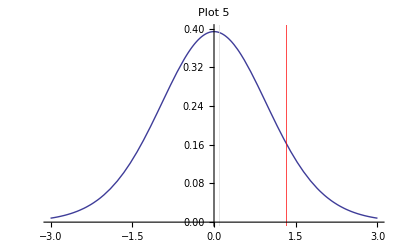

```mathematica
plot5=Plot[PDF[StudentTDistribution[19],x],{x,-3,3},GridLines->{{{.0989976,{Dashed,Thick}},{1.328,Red}},{1}},PlotRange->{0,.4},PlotLabel->"Plot 5"]
```

This plot shows that we are clearly not in the regection region so we cannot reject H_othat the proportion of US consumption to GDP is less than or equal to 75%.

### Testing that p is in the range of [50%,90%]

```mathematica
{(p̂-.5)/(√((.5(.5))/20)),(p̂-.9)/(√((.5(.5))/20))}
```

{3.09342,-0.484292}

```mathematica
CDF[StudentTDistribution[19],-.0484292]
```

0.48094

```mathematica
CDF[StudentTDistribution[19],3.09342]
```

0.997009

```mathematica
0.9970089002749891-0.48093982316785483
```

0.516069

The probabliity that the real proportion is between [50%,90%] is .516069

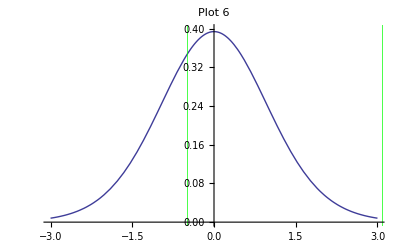

```mathematica
plot6=Plot[PDF[StudentTDistribution[19],x],{x,-3,3},GridLines->{{{-.484292,Green},{3.09342,Green}},{1}},PlotRange->{0,.4},PlotLabel->"Plot 6"]
```

## Part 4- Comparative Analysis

Estimated Difference of Means

### Point estimate of difference μ_1-μ_2 where μ_1 represents US GDP and μ_2represents US Disposable Income at an α=.95 level (corresponds to an α ± 2.086)

```mathematica
Mean[usgdp]-Mean[usdisposable]
```

1.75143×10^12

```mathematica
{(Mean[usgdp]-Mean[usdisposable])-2.086*(√(Variance[usgdp]/20+Variance[usdisposable]/20)),(Mean[usgdp]-Mean[usdisposable])+2.086*(√(Variance[usgdp]/20+Variance[usdisposable]/20))}
```

{2.16981×10^11,3.28588×10^12}

At the 95% confidence level we can say that hte range of exptected values for the difference in US GDP and US consumption is {2.16981×10^11,3.28588×10^12}.

### Hypothesis test that GDP is more than 2 * 10^12 more than us GDP

H_o:μ_1-μ_2=2 * 10^12
H_a:μ_1-μ_2≥ 2 * 10^12
α=.95, t_α value of 1.729

```mathematica
((Mean[usgdp]-Mean[usdisposable])-2 *10^12)/(√(Variance[usgdp]/20+Variance[usdisposable]/20))
```

-0.337914

```mathematica
1-CDF[StudentTDistribution[19],-0.33791429695559866]
```

0.630434

In this case we fail to reject H_0and must say that at the α=.95 level that US GDP is at least 2 Trillion dollars more than US Disposable income. The p-value associated with our test statistic is 0.630434.

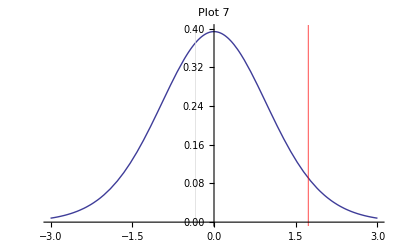

```mathematica
plot7=Plot[PDF[StudentTDistribution[19],x],{x,-3,3},GridLines->{{{-.337914,{Dashed,Thick}},{1.729,Red}},{1}},PlotRange->{0,.4},PlotLabel->"Plot 7"]
```

### Determining the probability that the difference between GDP and Disposable income is in the following range [0,2 Trillion]

```mathematica
{((Mean[usgdp]-Mean[usdisposable])-0)/(√(Variance[usgdp]/20+Variance[usdisposable]/20)),((Mean[usgdp]-Mean[usdisposable])-2 10^12)/(√(Variance[usgdp]/20+Variance[usdisposable]/20))}
```

{2.38097,-0.337914}

```mathematica
CDF[StudentTDistribution[19],-0.337914]
```

0.369566

```mathematica
CDF[StudentTDistribution[19],2.38097]
```

0.986057

```mathematica
0.9860571005233421-0.3695664962445486
```

0.616491

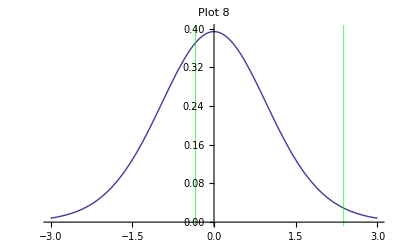

```mathematica
plot8=Plot[PDF[StudentTDistribution[19],x],{x,-3,3},GridLines->{{{-.337914,Green},{2.38097,Green}},{1}},PlotRange->{0,.4},PlotLabel->"Plot 8"]
```

The probabliity that the difference between US GDP and US Disposable income is between [0, 2 trillion] is 0.616491.

Estimated Ratio of Variances

### A point estimate and confidence interval at the α=.10 level for the ratio of variances between US GDP from 1990 to 2009 and US GDP from 1929-1945. I chose this time period to compare to because it was a time of extreme variance/volitility in GDP due to the great depression and World War II. This means that σ_1^2/σ_2^2~F(20,17),where 1 corresponds to recent and 2 to depression.

```mathematica
Variance[usgdp]/Variance[depressiongdp]
```

2852.23

```mathematica
1.86/2852.233644683513
```

0.00065212

The lower bound on our ratio with a 90% confidence is 0.00065212.

### Hypothesis test that the ratio between variances is greater than 2500.

H_0:σ^2/σ^2=2500
H_a:σ^2/σ^2>2500
α=.95

```mathematica
Variance[usgdp]/Variance[depressiongdp]*1/2500
```

1.14089

```mathematica
1-CDF[FRatioDistribution[20,17],1.1408934578734051]
```

0.395334

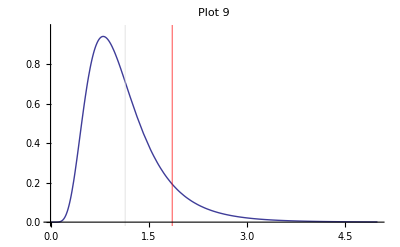

```mathematica
plot9=Plot[PDF[FRatioDistribution[20,17],x],{x,0,5},GridLines->{{{1.14089,{Dashed,Thick}},{1.86,Red}},{1}},PlotRange->{0,.98},PlotLabel->"Plot 9"]
```

The P-value associated with our test is 0.395334, which means we are not in the rejection region and cannot reject H_o.

### Finding the probability that the range of variances is between [1500,3000]

```mathematica
Variance[usgdp]/Variance[depressiongdp]*1/1500
```

1.90149

```mathematica
Variance[usgdp]/Variance[depressiongdp]*1/3000
```

0.950745

```mathematica
CDF[FRatioDistribution[20,17],0.9507445482278376]
```

0.452407

```mathematica
CDF[FRatioDistribution[20,17],1.9014890964556752]
```

0.907213

```mathematica
0.9072133952789283-0.4524068860577526
```

0.454807

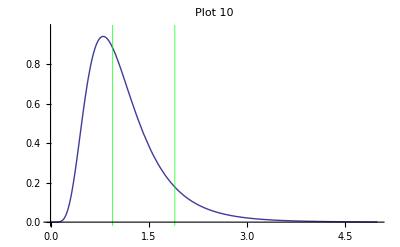

```mathematica
plot10 =Plot[PDF[FRatioDistribution[20,17],x],{x,0,5},GridLines->{{{.95074454,Green},{1.901489,Green}},{1}},PlotRange->{0,.98},PlotLabel->"Plot 10"]
```

The probability that the ratio is between 1500 and 3000 times is 0.454807.

Estimated Difference of Proportions

### I am going to be looking at the difference in the GDP Growth rate and the money suppy growth rate. I will provide a confidence interval at the α=.95 level.

```mathematica
Mean[newgdpgrowth]-Mean[newmoneyrate]
```

0.0555089

```mathematica
√((Mean[gdpgrowth]*(1-Mean[gdpgrowth]))/(Variance[gdpgrowth]/20)+(Mean[moneyrate]*(1-Mean[moneyrate]))/(Variance[moneyrate]/20))
```

0.+6.77772 ⅈ

```mathematica
1.79*√((Mean[newgdpgrowth]*(1-Mean[newgdpgrowth]))/(Variance[gdpgrowth]/20)+(Mean[newmoneyrate]*(1-Mean[newmoneyrate]))/(Variance[moneyrate]/20))
```

0.962442

The point estimate for the difference in proportions is .0555. The expected range of values for the difference in proportions is [0, .096]

### Hypothesis test that p_1-p_2>0.

H_0:p_1-p_2=0
H_a: p_1-p_2>0
α=.95

```mathematica
(Mean[newgdpgrowth]-Mean[newmoneyrate])/(√((Mean[newgdpgrowth]*(1-Mean[newgdpgrowth]))/(Variance[gdpgrowth]/20)+(Mean[newmoneyrate]*(1-Mean[newmoneyrate]))/(Variance[moneyrate]/20)))
```

0.00103238

```mathematica
CDF[StudentTDistribution[19],0.0010323838839371249]
```

0.500406

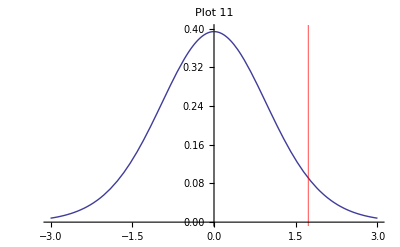

```mathematica
plot11=Plot[PDF[StudentTDistribution[19],x],{x,-3,3},GridLines->{{{-.00103238,{Dashed,Thick}},{1.729,Red}},{1}},PlotRange->{0,.4},PlotLabel->"Plot 11"]
```

We fail to reject H_0 and say that accoding to our data, at the .95 confidence interval the GDP growth rate and Money supply growth rate are the same.

### Probabliity that the range of differences is between [-.05,.05]

```mathematica
((Mean[newgdpgrowth]-Mean[newmoneyrate])+.05)/(√((Mean[newgdpgrowth]*(1-Mean[newgdpgrowth]))/(Variance[gdpgrowth]/20)+(Mean[newmoneyrate]*(1-Mean[newmoneyrate]))/(Variance[moneyrate]/20)))
```

0.094025

```mathematica
((Mean[newgdpgrowth]-Mean[newmoneyrate])-.05)/(√((Mean[newgdpgrowth]*(1-Mean[newgdpgrowth]))/(Variance[gdpgrowth]/20)+(Mean[newmoneyrate]*(1-Mean[newmoneyrate]))/(Variance[moneyrate]/20)))
```

-0.0919602

```mathematica
CDF[StudentTDistribution[19],-0.09196019002469066]
```

0.463846

```mathematica
CDF[StudentTDistribution[19],0.09402495779256491]
```

0.536963

```mathematica
0.5369630979238279-0.46384617169590525
```

0.0731169

The probility that the proportions are in the range of [-.05 , .05] is 0.0731169.

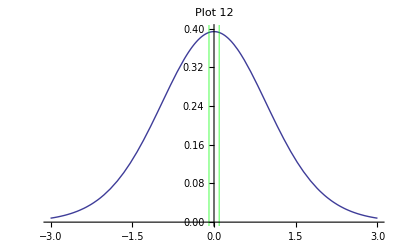

```mathematica
plot12=Plot[PDF[StudentTDistribution[19],x],{x,-3,3},GridLines->{{{-.0919602,Green},{.094025,Green}},{1}},PlotRange->{0,.4},PlotLabel->"Plot 12"]
```

```mathematica
Table[{plot1,plot2,plot3,plot4,plot5,plot6,plot7,plot8,plot9,plot10,plot11,plot12}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}